```mathematica
(*Режим непрерывной накчки*)
```

```mathematica
Experiment1=({{"Ток накачки, A", "Напряжение, В", "Показания калориметра, Дж"}, {2.1, 6, 49}, {1.9, 6, 46}, {1.8, 6, 45}, {1.7, 6, 43}, {1.6, 6, 41}, {1.5, 6, 36}, {1.4, 6, 32}, {1.3, 6, 29}, {1.2, 6, 25}, {1.1, 6, 21}, {1.0, 6, 17}});
Experiment1Extended=Append[Transpose[Experiment1],Join[{"Показания ИМЛ, Вт"},N[Experiment1[[2;;12,3]]*270*10^-4]]];
Experiment1Extended=Transpose[Experiment1Extended];
Grid[Experiment1Extended, Frame->All]
```

Ток накачки, A | Напряжение, В | Показания калориметра, Дж | Показания ИМЛ, Вт
2.1 | 6 | 49 | 1.323
1.9 | 6 | 46 | 1.242
1.8 | 6 | 45 | 1.215
1.7 | 6 | 43 | 1.161
1.6 | 6 | 41 | 1.107
1.5 | 6 | 36 | 0.972
1.4 | 6 | 32 | 0.864
1.3 | 6 | 29 | 0.783
1.2 | 6 | 25 | 0.675
1.1 | 6 | 21 | 0.567
1. | 6 | 17 | 0.459

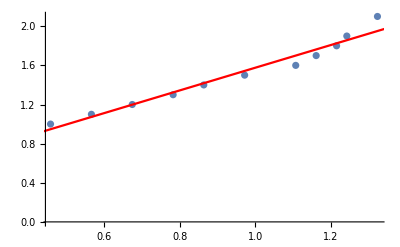

```mathematica
PlotPartExperiment1=Transpose[{Experiment1Extended[[2;;12]][[All,1]]}].({{0, 1}})+Transpose[{Experiment1Extended[[2;;12]][[All,4]]}].({{1, 0}});
PlotPartExperiment1Fit=LinearModelFit[PlotPartExperiment1,x,x];
Show[ListPlot[PlotPartExperiment1],Plot[PlotPartExperiment1Fit["BestFit"],{x,0,1.5},PlotStyle->Red]]
```